Indeksi cen stanovanjskih nepremičnin po vrstah stanovanjskih nepremičnin, Slovenija, četrtletno

## Pridobivanje prvotnih podatkov iz SURS-a

```mathematica
podatki2=Import[NotebookDirectory[]<>"podatki.csv", "Table", "FieldSeparators"->";", HeaderLines->2, CharacterEncoding->"WindowsEastEurope"]//ResourceFunction["DatasetWithHeaders"]
```

## Primerjava posameznih vrst nepremičnin z njihovimi indeksi po letih za četrtletje Q1 iz prvotne tabele

```mathematica
podatkiSamoQ1=Import[NotebookDirectory[]<>"podatki2.csv", "Table", "FieldSeparators"->";", HeaderLines->3, CharacterEncoding->"WindowsEastEurope"]//Prepend[#,{"Vrsta nepremičnine","2007", "2008", "2009","2010","2011","2012","2013","2014","2015","2016","2017","2018","2019","2020","2021"}]&//ResourceFunction["DatasetWithHeaders"]
```

```mathematica
(*povsod, kjer so bile ..., sem zamenjala z 0 in dodala stolpcem imena*)
```

```mathematica
zNiclo = podatkiSamoQ1//Query[All,<|#, "2007"->If[#"2007"=="...",0,#"2007"],"2008"->If[#"2008"=="...",0,#"2008"],"2009"->If[#"2009"=="...",0,#"2009"],"2010"->If[#"2010"=="...",0,#"2010"],"2011"->If[#"2011"=="...",0,#"2011"],"2012"->If[#"2012"=="...",0,#"2012"],"2013"->If[#"2013"=="...",0,#"2013"],"2014"->If[#"2014"=="...",0,#"2014"],"2015"->If[#"2015"=="...",0,#"2015"],"2016"->If[#"2016"=="...",0,#"2016"],"2017"->If[#"2017"=="...",0,#"2017"],"2018"->If[#"2018"=="...",0,#"2018"],"2019"->If[#"2019"=="...",0,#"2019"],"2020"->If[#"2020"=="...",0,#"2020"],"2021"->If[#"2021"=="...",0,#"2021"]|>&]
```

```mathematica
(*naredim graf, ki prikazuje padec in dvig indeksov, tisti, ki so nad 100 pomeni rast, pod 100 pa padec*)
```

```mathematica
(*izberem samo vse podatke (All) iz vstice 2 (Nove stanovanjske nepremičnine)*)
```

## Nove stanovanjske nepremičnine

```mathematica
(* KB: Transpose dodan pri uvozu, leta morajo biti številke, da jih ListLinePlot nariše *)
```

```mathematica
podatki=Import[NotebookDirectory[]<>"podatki2.csv", "Table", "FieldSeparators"->";", HeaderLines->2, CharacterEncoding->"WindowsEastEurope"];
(* KB: Za leta vzamemo prvo vrstico pred transponiranjem, kjer so leta v glavi, izpustimo prvo celico, ter vzamemo prve štiri znake, ki so ravno leto. ToExpression za naše potrebe spremeni niz v število. *)
leta=podatki//First//Rest//StringTake[#,4]&//ToExpression//Prepend[#,"Leto"]&;
```

```mathematica
vsi=podatki//Prepend[#,leta]&//Transpose//ResourceFunction["DatasetWithHeaders"]//Query[All,{1,4}]
```

```mathematica
MaximalBy[vsi,"1.1 Nove stanovanjske nepremičnine"]
```

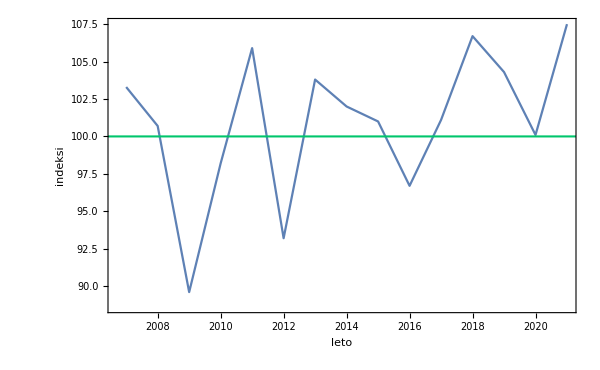

```mathematica
ListLinePlot[vsi,GridLines->{None,{100}},GridLinesStyle->Directive[AbsoluteThickness[3/2],ColorData[96,8]],Frame->True,FrameLabel->{{"indeksi",""},{"leto","Nove stanovanjske nepremičnine"}},BaseStyle->{FontSize->15},ImageSize->600]
```

```mathematica
(*Vse kar je pod 100 pomeni izguba v primerjavi s prejšnjim letom?*)
```

## Rabljene stanovanjske nepremičnine

```mathematica
podatki=Import[NotebookDirectory[]<>"podatki2.csv", "Table", "FieldSeparators"->";", HeaderLines->2, CharacterEncoding->"WindowsEastEurope"];
leta=podatki//First//Rest//StringTake[#,4]&//ToExpression//Prepend[#,"Leto"]&;
vsiRabljeni=podatki//Prepend[#,leta]&//Transpose//ResourceFunction["DatasetWithHeaders"]//Query[All,{1,7}]
```

```mathematica
MaximalBy[vsiRabljeni,"1.2 Rabljene stanovanjske nepremičnine"]
```

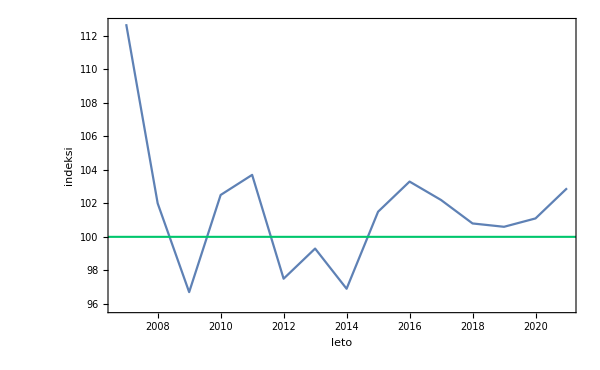

```mathematica
ListLinePlot[vsiRabljeni,GridLines->{None,{100}},GridLinesStyle->Directive[AbsoluteThickness[3/2],ColorData[96,8]],Frame->True,FrameLabel->{{"indeksi",""},{"leto","Rabljene stanovanjske nepremičnine"}},BaseStyle->{FontSize->15},ImageSize->600]
```

### Transponirana prvotna tabela

```mathematica
transponirana=Import[NotebookDirectory[]<>"podatki2.csv", "Table", "FieldSeparators"->";", HeaderLines->2, CharacterEncoding->"WindowsEastEurope"]//Transpose//Map[If[#=="...",0,#]&,#,{2}]&//ResourceFunction["DatasetWithHeaders"]//Query[All,<|"Leto"->ToExpression[StringTake[#"STANOVANJSKE NEPREMIČNINE",4]], #|>&]//KeyDrop["STANOVANJSKE NEPREMIČNINE"]
```

## Največji in najmanjši indeks cen za posamezno vrsto stanovanjskih nepremičnin

### Računanje največje vrednosti za posamezno vrsto nepremičnine

```mathematica
najvecjaVrednostSKUPAJ=transponirana//Normal//Query[All,"1 Stanovanjske nepremičnine - SKUPAJ"]//Max
```

109.2

```mathematica
najvecjaVrednostZaNove=transponirana//Normal//Query[All,"1.1 Nove stanovanjske nepremičnine"]//Max
```

107.5

```mathematica
najvecjaVrednostZaRabljene=transponirana//Normal//Query[All,"1.2 Rabljene stanovanjske nepremičnine"]//Max
```

112.7

### Računanje najmanjše vrednosti za posamezno vrsto nepremičnine

```mathematica
najmanjsaVrednostSKUPAJ=transponirana//Normal//Query[All,"1 Stanovanjske nepremičnine - SKUPAJ"]//Min
```

93.8

```mathematica
najmanjsaVrednostZaNove=transponirana//Normal//Query[All,"1.1 Nove stanovanjske nepremičnine"]//Min
```

89.6

```mathematica
najmanjsaVrednostZaRabljene=transponirana//Normal//Query[All,"1.2 Rabljene stanovanjske nepremičnine"]//Min
```

96.7

### Tabela največjih in najmanjših vrednosti

```mathematica
Dataset[<|"1 Stanovanjske nepremičnine - SKUPAJ"-><|"Leto"->2009,"Najmanjši indeks"->najmanjsaVrednostSKUPAJ|>,"1.1 Nove stanovanjske nepremičnine"-><|"Leto"->2009,"Najmanjši indeks"->najmanjsaVrednostZaNove|>,
"1.2 Rabljene stanovanjske nepremičnine"-><|"Leto"->2009,"Najmanjši indeks"->najmanjsaVrednostZaRabljene|>|>]
```

```mathematica
data1=Dataset[<|"1 Stanovanjske nepremičnine - SKUPAJ"-><|"Leto"->2007,"Največji indeks"->najvecjaVrednostSKUPAJ|>,"1.1 Nove stanovanjske nepremičnine"-><|"Leto"->2021,"Največji indeks"->najvecjaVrednostZaNove|>,
"1.2 Rabljene stanovanjske nepremičnine"-><|"Leto"->2007,"Največji indeks"->najvecjaVrednostZaRabljene|>|>]
```